```mathematica
Needs["queues`"];
```

```mathematica
Needs["drawTx`"]
```

```mathematica
Needs["simulateTx`"]
```

```mathematica
RandExp[x_]:=-1/x*Log[Random[Real]];
```

# Practica II

## Análisis del trhoughput a lo largo de la transimisión

```mathematica
ThAcum[lpkt_]:=Map[{#[[1]],#[[3]]/#[[1]]}&,lpkt]
```

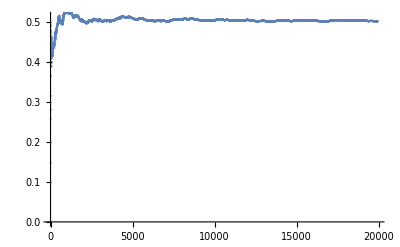

```mathematica
sim=LaunchSimTxSW[RandExp[0.5],0,0,10000,RandExp[3]];
th=ThAcum[sim];
ListPlot[th]
```

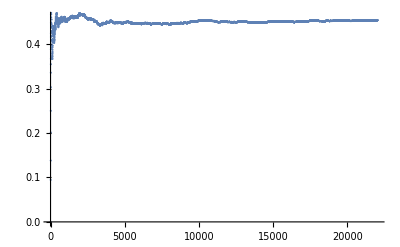

```mathematica
ListPlot[QueueThAcum[Queue1Sim[RandExp[0.1/0.22],RandExp[(1-0.16)/(3*0.22)],10000]]]
```

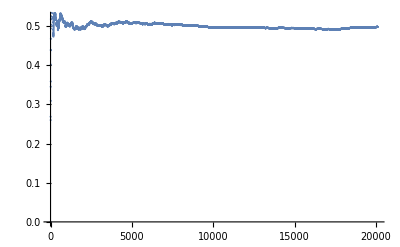

```mathematica
ListPlot[ThAcum[LaunchSimTxGBN[RandExp[0.5],0,0,10000,RandExp[3]]]]
```

Stop & Wait

## Throughput teórico máximo según a p ti

```mathematica
ThMaxSW[a_,p_,ti_]:=(1-p)/(a*ti)//N;
```

## Througput teórico en función de a

```mathematica
Manipulate[Show[Plot[ThMaxSW[ax,p,ti],{ax,1,10}],ListPlot[{{a,Last[ThAcum[LaunchSimTxSW[ti*ro,(a-1)/2,p,1000,ti]]][[2]]}}]],{a,1,10},{p,0,1},{ti,0.1,2},{ro,0.1,1}]
```

## Througput teórico en función de p

```mathematica
Manipulate[Show[Plot[ThMaxSW[a,px,ti],{px,0,1}],ListPlot[{{p,Last[ThAcum[LaunchSimTxSW[ti*ro,(a-1)/2,p,1000,ti]]][[2]]}}]],{a,1,10},{p,0,1},{ti,0.1,2},{ro,0.1,1}]
```

## Througput teórico en función de ro (comparación con M/M/1)

```mathematica
Manipulate[
Show[Plot[x,{x,0,1.5}],
ListPlot[{{
Last[ThAcum[LaunchSimTxSW[RandExp[ro/ti],(a-1)/2,p,1000,RandExp[1/ti]]]][[2]],
Last[QueueThAcum[Queue1Sim[RandExp[ro/ti],RandExp[(1-p)/(a*ti)],1000]]][[2]]
}}]
]
,{a,1,10},{p,0,1},{ti,0.1,2},{ro,0.1,1}]
```

Go Back N

## Throughput teórico máximo según a p ti

```mathematica
ThMaxGBN[a_,p_,ti_]:=((1-p)/(ti*(1+(a-1)*p)))//N;
```

## Througput teórico en función de a

```mathematica
Manipulate[Show[Plot[ThMaxGBN[ax,p,ti],{ax,1,10}],ListPlot[{{a,Last[ThAcum[LaunchSimTxGBN[ti*ro,(a-1)/2,p,1000,ti]]][[2]]}}]],{a,1,10},{p,0,1},{ti,0.1,2},{ro,0.1,1}]
```

## Througput teórico en función de p

```mathematica
Manipulate[Show[Plot[ThMaxGBN[a,px,ti],{px,0,1}],ListPlot[{{p,Last[ThAcum[LaunchSimTxGBN[ti*ro,(a-1)/2,p,1000,ti]]][[2]]}}]],{a,1,10},{p,0,1},{ti,0.1,2},{ro,0.1,1}]
```

## Througput teórico en función de ro (comparación con M/M/1)

```mathematica
Manipulate[
Show[Plot[x,{x,0,1.5}],
ListPlot[{{
Last[ThAcum[LaunchSimTxGBN[RandExp[ro/ti],(a-1)/2,p,1000,RandExp[1/ti]]]][[2]],
Last[QueueThAcum[Queue1Sim[RandExp[ro/ti],RandExp[(1-p)/(ti*(1+(a-1)*p))],1000]]][[2]]
}}]
]
,{a,1,10},{p,0,1},{ti,0.1,2},{ro,0.1,1}]
```

Muestra visual

```mathematica
SetIniParDraw[1,0]
```

```mathematica
lineaSW=LaunchSimTxSW[RandExp[1.5],1,0.5,20,RandExp[0.5]];
```

```mathematica
Manipulate[Show[DrawWin[tw,ww,10],Map[(DrawPacketTx[#])&,SelectPacketInWin[lineaSW]]],{tw,0,100},{ww,0.01,10}]
```

```mathematica
lineaGBN=LaunchSimTxGBN[RandExp[1.5],1,0.4,20,RandExp[0.5]];
```

```mathematica
Manipulate[Show[DrawWin[tw,ww,10],Map[(DrawPacketTx[#])&,SelectPacketInWin[lineaGBN]]],{tw,0,100},{ww,0.01,10}]
```